# Periodic Orbits

The VDP system has one periodic orbit and the Rosseler system looks like it might have periodic orbits.  First we need to define a periodic orbit and a thing called a winding number.

Orbit of ODE (Informal Definition)
The solution of an ODE y'=f(y) defined by a choice of y(0)=y_0 is called an orbit.

Periodic Orbit of ODE (Informal Definition)
An orbit of the ODE y'=f(y) is periodic if for some T>0 we have  y(t)=y(t+T) for all t.The period is the smallest possible T.

Map (Informal Definition)
A map is function g:ℝ^n→ℝ^n. An orbit is the sequence y_(k+1)=g(y_k) defined by a choice of y_0∈ℝ^n.

Periodic Orbit of Map (Informal Definition)
The orbit y_(k+1)=g(y_k) is periodic if for some K≥1 we have y_k=y_(k+K) for all k.  The period is the smallest possible K.

## Periodic Orbits for VDP

The VDP system is
	y1' | = | y2                               
y2' | = | μ(1-y1^2)y2-y1
clearly has a periodic orbit which sucks all the solutions in.  We can approximate a point on this periodic orbit by running the ODE solver and grabbing any value well out in the orbit.

```mathematica
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
Df[μ_][{x_,v_}]:={{0,1},{-1-2v x μ,μ (1-x^2)}}
TMax=64.5;y0={0,0.1};μ=0.2; ϵ=1;
ySol=NDSolveValue[{
y'[t]==f[μ][y[t]],y[0]==y0
},y,{t,0, TMax}
];
TabView[{
"Phase Space"->ParametricPlot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]],
"y_1& y_2"->Plot[ySol[t],{t, 0, TMax},
PlotLabel->ySol[TMax]]
},2]
```

12

We can estimate the period from a graph and find

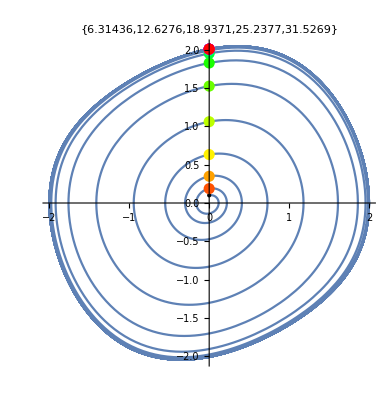

```mathematica
ParametricPlot[ySol[t],{t,0, TMax},
Epilog->{{Black,Point[ySol[0]]},Table[{Hue[i/Length[Data]],PointSize[0.02],Point[Data⟦i,2⟧]},{i,Length[Data]}]},
PlotLabel->Data⟦1;;5,1⟧]
```

## Intro First Return Map for Rosseller System y_1==0

The same trick for the  Rosseler system.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};  TMax=54;
y0={0,1.7,14.6};
{Hmm,{Data}}=Reap[{ySol,JSol}=NDSolveValue[{
y'[t]==f[StdParams][y[t]],y[0]==y0,
J'[t]==df[StdParams][y[t]].J[t], J[0]==({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
},{y,J},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1,
"EventAction":> Sow[{t, y[t], J[t]}]}];
];
BasePic=Show[
ParametricPlot3D[ySol[t],{t,0, TMax},
PlotRange->All],
Graphics3D[{Black,PointSize[0.02],Point[ySol[0]]}],
Graphics3D[{Opacity[0.5],Yellow,Polygon[15{{0,-1,0},{0,1,0},{0,1,2},{0,-1,2}}]}]];
Dots=Graphics3D[{PointSize[0.02],Table[{Hue[i/Length[Data]],Point[Data⟦i,2⟧]},{i,Length[Data]}]},
Axes->True,BoxRatios->{1, 1, 1}];
TabView[{
"y"->BasePic,
"y+"->Show[BasePic,Dots,PlotLabel->Data⟦All,1⟧],
"Dots"->Dots
}]
```

123

## Pic: First Return Map for VDP System y_1==0

Our VDP system is
	y1' | = | y2                               
y2' | = | μ(1-y1^2)y2-y1
I am going to look at initial conditions y_0=(0,x) and catch the output y_*=(0,r(x)) the first time it crosses y_1==0 heading in the same direction. In Mathematica there is a way to catch stop the ODE solver at an “event”. In Mathematica there is also a way to easily put parameters into ODE solvers. It looks like this.

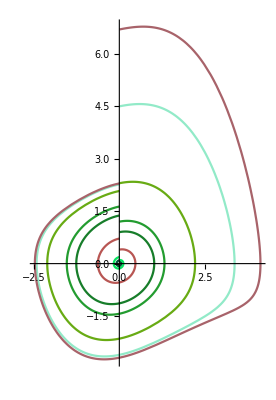

```mathematica
Clear[μ,x,f,Df]
f[μ_][{x_,v_}]:={v,μ (1-x^2)v-x}
μ=0.2;
TMax=12;
ySol=ParametricNDSolveValue[{y'[t]==f[μ][y[t]],y[0]=={0,x}},y,{t, 0,TMax},x,
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1}];
xVals={0.05,.1,0.4,0.9,1.2,2.3,4.5,6.7};
Show[Table[
p=ySol[x];
tEnd=p["Domain"][[1,2]];
ParametricPlot[p[t],{t,0,tEnd},PlotStyle->RandomColor[]],
{x,xVals}],PlotRange->All]
```

All we really want out of this is the last computed y value.

ParametricFunction[<>]

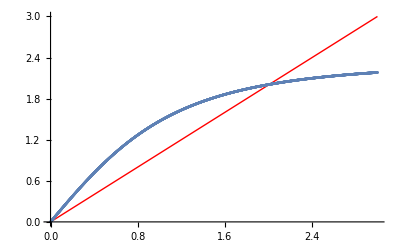

```mathematica
Clear[x,y,t]
ySol=ParametricNDSolveValue[{y'[t]==f[μ][y[t]],y[0]=={0,x}},y,{t, 0,TMax},x,
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1}]
{xMin,xMax,Δx}={0.001,3,0.001};
OutputVals=Table[ySol[x]["ValuesOnGrid"]⟦-1⟧,{x, xMin,xMax,Δx}];
ListPlot[ OutputVals⟦All,2⟧,PlotRange->{{0,xMax},{0,xMax}},DataRange->{xMin,xMax},Prolog->{Red,Line[{{0,0},{xMax,xMax}}]}]
```

This is a pretty boring curve!  What it tells you is that all curves squish into the curve that starts at the crossing point.  The convergence is monotone: if we start below the crossing point we head up; if we start below we head down. It does not jump around at all

## Pic: First Return Map for Rosseller System y_1==0

The Rosseler map is easier to plot because it jumps around.  I can just start it anywhere and eventually I will get a lot of points.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};  TMax=5400;
y0={0,1.7,14.6};
{Hmm,{Data}}=Reap[NDSolveValue[{
y'[t]==f[StdParams][y[t]],y[0]==y0
},{},{t,0, TMax},
Method->{"EventLocator", "Event":>y[t]⟦1⟧==0,"Direction"->1,
"EventAction":> Sow[y[t]]}];
];
m=Length[Data];
TabView[{
"y"->ListPlot[Data⟦All,2⟧,AxesLabel->{"t","y"}],
"z"->ListPlot[Data⟦All,3⟧,AxesLabel->{"t","z"}],
"y vs z"->Graphics[Table[
{Hue[0.8*i/m],PointSize[0.005],Point[Data⟦i,2;;3⟧]},{i, m}],
AxesLabel->{"y","z"},
Axes->True,AspectRatio->1,PlotLabel->m]
}]
```

NDSolveValue::noout: No functions were specified for output from NDSolveValue.

123

We expected it to be skinny but it almost looks like a curve.  We are going to spend a while explaining why it can not be a curve! We may spend even more time explaining what it can be if it is not a curve. Since it looks 1D we are going to try to look at it in a 1D way.

## Pic: Fancy Sort Of First Return Map for Rosseller System y_3 Hill Top!

The top of the hill is easy to pick out on each Rosseler loop!  We can look at what happens to the height of the hill each time it loops.  It looks like it goes up a little bit each time until it drops down suddenly, To get the top I need to change the “direction”.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};  TMax=540;
y0={0,1.7,14.6};
{Hmm,{Data}}=Reap[NDSolveValue[{
y'[t]==f[StdParams][y[t]],y[0]==y0
},{},{t,0, TMax},
Method->{"EventLocator", "Event":>y'[t]⟦3⟧==0,"Direction"->-1,
"EventAction":> Sow[y[t]]}];
];
m=Length[Data];
TabView[{
"y"->ListPlot[Data⟦All,2⟧,AxesLabel->{"t","y"}],
"z"->ListPlot[Data⟦All,3⟧,AxesLabel->{"t","z"}],
"y vs z"->Graphics[Table[
{Hue[0.9*i/m],PointSize[0.005],Point[Data⟦i,2;;3⟧]},{i, m}],
AxesLabel->{"y","z"},
Axes->True,AspectRatio->1,PlotLabel->m],
"(y,z)→(y,z)"->Graphics[Table[
{Hue[0.9*i/m],Thickness[0.001],Arrow[{Data⟦i,2;;3⟧,Data⟦i+1,2;;3⟧}]},{i, m-1}],
AxesLabel->{"y","z"},
Axes->True,AspectRatio->1,PlotLabel->m]
},4]
```

NDSolveValue::noout: No functions were specified for output from NDSolveValue.

1234

Looks like it is stuck in an “almost” loop! How do we get more data?

## Pic: Fancy Sort Of First Return Map for Rosseller System y_3 Hill Top!

The top of the hill is easy to pick out on each Rosseler loop!  We can look at what happens to the height of the hill each time it loops.  It looks like it goes up a little bit each time until it drops down suddenly, To get the top I need to change the “direction”.

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={0.2,0.2,5.7};  TMax=540;
y0={0,1.7,14.6};
{Hmm,{Data}}=Reap[NDSolveValue[{
y'[t]==f[StdParams][y[t]],y[0]==y0
},{},{t,0, TMax},
Method->{"EventLocator", "Event":>y'[t]⟦3⟧==0,"Direction"->-1,
"EventAction":> Sow[y[t]]}];
];
m=Length[Data];
TabView[{
"y"->ListPlot[Data⟦All,2⟧,AxesLabel->{"t","y"}],
"z"->ListPlot[Data⟦All,3⟧,AxesLabel->{"t","z"}],
"y vs z"->Graphics[Table[
{Hue[0.9*i/m],PointSize[0.005],Point[Data⟦i,2;;3⟧]},{i, m}],
AxesLabel->{"y","z"},
Axes->True,AspectRatio->1,PlotLabel->m],
"(y,z)→(y,z)"->Graphics[Table[
{Hue[0.9*i/m],Thickness[0.001],Arrow[{Data⟦i,2;;3⟧,Data⟦i+1,2;;3⟧}]},{i, m-1}],
AxesLabel->{"y","z"},
Axes->True,AspectRatio->1,PlotLabel->m]
},4]
```

NDSolveValue::noout: No functions were specified for output from NDSolveValue.

1234

Looks like it is stuck in an “almost” loop! How do we get more data?

There is another way to make the same data since 
	  y3'=b  + y3(y1-c)=0
All the points we are computing lie on this surface

```mathematica
Clear[ f,df,y1,y2,y3,a,b,c]
f[{a_,b_,c_}][{y1_,y2_,y3_}]:= {-y2-y3,y1+ a y2, b  + y3(y1-c)}
df[{a_,b_,c_}][{y1_,y2_,y3_}]:={{0,-1,-1},{1,a,0},{y3,0,-c+y1}}
StdParams={a,b,c}={0.2,0.2,5.7};  TMax=54;
y0={0,1.7,14.6};
ySol=NDSolveValue[{
y'[t]==f[StdParams][y[t]],y[0]==y0
},y,{t,0, TMax}
]
Show[
ContourPlot3D[ b+y3(y1-c)==0, {y1,-12,12},{y2,-12,12},{y3,0, 30},ContourStyle->Opacity[0.2]],ParametricPlot3D[ySol[t],{t,0, TMax},PlotRange->All],
AxesLabel->{"y1","y2","y3"}
]
```